## 3. Rotation Matrix

```mathematica
Clear["Global`*"]
```

A rotation matrix is a square matrix that represents a rotation of a coordinate frame or a vector in space. It describes how the axes of a rotated frame are oriented relative to a fixed reference frame. Let’s define functions that represents rotations around the 3 axis. 
To insert greek letters, use Esc+letter+Esc. Example Esc+a+Esc = α

```mathematica
Rx[α_]={{1, 0, 0},{0,Cos[α],-Sin[α]},{0, Sin[α],Cos[α]}}; (*Rotation around x*)
Ry[α_] = {{Cos[α], 0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}}; (*Rotation around y*)
Rz[α_] = {{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0,0,1}} (*Rotation around z*)
```

{{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}}

```mathematica
Rz[β]//MatrixForm
```

(Cos[β] | -Sin[β] | 0
Sin[β] | Cos[β] | 0
0 | 0 | 1)

One of the properties of the rotation matrices is that they are orthogonal: Inverse[M] = Transpose[M]. Let’s show it

```mathematica
Mzinv = Inverse[Rz[β]];
Mzinv // MatrixForm
```

(Cos[β]/(Cos[β]^2+Sin[β]^2) | Sin[β]/(Cos[β]^2+Sin[β]^2) | 0
-Sin[β]/(Cos[β]^2+Sin[β]^2) | Cos[β]/(Cos[β]^2+Sin[β]^2) | 0
0 | 0 | 1)

```mathematica
Mzinv = Simplify[Mzinv];
Mzinv // MatrixForm
```

(Cos[β] | Sin[β] | 0
-Sin[β] | Cos[β] | 0
0 | 0 | 1)

As we anticipated, the input of the function as been defined as w_ and this allow us to insert what we like. Let’s try to put some numbers. Like π/4. To write π use Esc+pi+Esc.

```mathematica
Rz[π/4] // MatrixForm
```

(1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1)

If you want to compute the numerical approximation of those ratios, use N in front of the function.

```mathematica
N[Rz[π/4]] // MatrixForm
```

(0.707107 | -0.707107 | 0.
0.707107 | 0.707107 | 0.
0. | 0. | 1.)

A combination of multiple rotation of generic angles can be expressed by:

```mathematica
R1=Simplify[Rx[α].Ry[β]];R1//MatrixForm
```

(Cos[β] | 0 | Sin[β]
Sin[α] Sin[β] | Cos[α] | -Cos[β] Sin[α]
-Cos[α] Sin[β] | Sin[α] | Cos[α] Cos[β])

Definition of Euler’s angles:

```mathematica
EulZXZ[θ1_,θ2_,θ3_]:=Rz[θ1].Rx[θ2].Rz[θ3]; (*Function that rotates a body given three Euler's agnels on the form RotZ-RotX-RotZ*)
```

```mathematica
EulZYZ[α1_,α2_,α3_]:=Rz[α1].Ry[α2].Rz[α3]; (*Function that rotates a body given three Euler's agnels on the form RotZ-RotY-RotZ*)
```

```mathematica
Simplify[EulZYZ[α,β,γ]]//MatrixForm
```

(Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ] | -Cos[γ] Sin[α]-Cos[α] Cos[β] Sin[γ] | Cos[α] Sin[β]
Cos[β] Cos[γ] Sin[α]+Cos[α] Sin[γ] | Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ] | Sin[α] Sin[β]
-Cos[γ] Sin[β] | Sin[β] Sin[γ] | Cos[β])

## 4. Homogeneous Transformation Matrix

This kind of transformation is adding a translation to a rotation. Let’s build a function that help me do that.

```mathematica
Mrotztrasl[α_, point_] := {{Cos[α], -Sin[α], 0, point[[1]]}, {Sin[α], Cos[α], 0, point[[2]]}, {0, 0, 1, point[[3]]}, {0, 0, 0, 1}}
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

It is possible to give as arguments of the function, some functions. For example, parameter that are functions of time

```mathematica
M01t=Mrotztrasl[α[t],{xO[t],yO[t],z0[t]}];
M01t//MatrixForm
```

(Cos[α[t]] | -Sin[α[t]] | 0 | xO[t]
Sin[α[t]] | Cos[α[t]] | 0 | yO[t]
0 | 0 | 1 | z0[t]
0 | 0 | 0 | 1)

```mathematica
M01tdot = D[M01t, t]; 
M01tdot // MatrixForm (* Matrix M01t derived overt time *)
```

(-Sin[α[t]] α'[t] | -Cos[α[t]] α'[t] | 0 | xO'[t]
Cos[α[t]] α'[t] | -Sin[α[t]] α'[t] | 0 | yO'[t]
0 | 0 | 0 | z0'[t]
0 | 0 | 0 | 0)

# Scara Robot Kinematic Analysis -Graphics-

## 1. Direct Kinematics

The goal is to compute the position of the end effector wrt the absolute reference frame which here is denoted as 0. To do this, we are going to find a sequence of rototranslation matrices and combine them together. We can consider the joint connections in the top view as the origins of the local reference frames. A is then going to the the origin of local reference frame 1 and P the same for local reference frame 2.

```mathematica
A = {L1 Cos[θ1[t]],L1 Sin[θ1[t]],h,1};
```

```mathematica
M01=Mrotztrasl[θ1[t],A[[1;;3]]];
```

```mathematica
M01//MatrixForm (*Transformation matrix from RF1 to RF0*)
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | L1 Cos[θ1[t]]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | L1 Sin[θ1[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

As an alternative, we can think that M01 is a transformation of the origin O0 produced by the sequence of a rotation around z0 and a translation along x1 and z1 .

```mathematica
Mrotztrasl[θ1[t],{0,0,0,1}].Mrotztrasl[0,{L1,0,h,1}]//MatrixForm
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | L1 Cos[θ1[t]]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | L1 Sin[θ1[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
P1={L2 Cos[θ2[t]],L2 Sin[θ2[t]],0,1}; (*Point P w.r.t.RF1*)
P = M01.P1; (*Position of P wrt RF0*)
P // Simplify// MatrixForm
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h
1)

```mathematica
M12=Mrotztrasl[θ2[t],P1[[1;;3]]];
M12 // MatrixForm
```

(Cos[θ2[t]] | -Sin[θ2[t]] | 0 | L2 Cos[θ2[t]]
Sin[θ2[t]] | Cos[θ2[t]] | 0 | L2 Sin[θ2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02 = M01.M12;
M02 // MatrixForm
```

(Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]] | -Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]] Cos[θ2[t]]-L2 Sin[θ1[t]] Sin[θ2[t]]
Cos[θ2[t]] Sin[θ1[t]]+Cos[θ1[t]] Sin[θ2[t]] | Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Cos[θ2[t]] Sin[θ1[t]]+L2 Cos[θ1[t]] Sin[θ2[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
M02=Simplify[M01.M12];
M02//MatrixForm(*Simplified version:the two joint variables are combined*)
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
E2={0,0,-L[t],1}; (*Point E w.r.t.RF2*)
```

```mathematica
M23=Mrotztrasl[0,E2⟦1;;3⟧];
M23//MatrixForm(*Transformation matrix from RF3 to RF2*)
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | -L[t]
0 | 0 | 0 | 1)

```mathematica
M03=M02.M23;
M03//MatrixForm(*The pose matrix of link 3 (the end effector)*)
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
EE=Simplify[M03.{0,0,0,1}];
EE//MatrixForm (*Point E w.r.t.RF0,which is the location of the end effector*)
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h-L[t]
1)

```mathematica
M03[[1;;4,4]] // MatrixForm (*alternative to extract the position of the end effector*)
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h-L[t]
1)

```mathematica
Data1={L1->0.3,L2->0.3,h->1,θ1[t]->0.2,θ2[t]->0.1,L[t]->0.3};N[M03/. Data1]//MatrixForm(*For instance,the link 3 configuration is found given the robot dimensions and a joint configuration*)
```

(0.955336 | -0.29552 | 0. | 0.580621
0.29552 | 0.955336 | 0. | 0.148257
0. | 0. | 1. | 0.7
0. | 0. | 0. | 1.)

Given a point projected in reference frame 0, through the inverse of M03 it is possible to find its coordinates in reference frame frame 3. For instance, point A :

```mathematica
A3=Simplify[Inverse[M03].A]
```

{-L2,0,L[t],1}

## 2. Inverse Kinematics

In Inverse kinematics the goal is to identify the positions of the joints such that I can achieve a desired position and orientation of the end effector. 
The desired pose of the end effector is described by matrix M03d (d stands for desired). Let’s assume that we need the end effector located at {xd,yd,zd} with orientation described by a simple rotation of ψd about z axis.

```mathematica
M03d=Mrotztrasl[ψd,{xd,yd,zd}];
M03d//MatrixForm
```

(Cos[ψd] | -Sin[ψd] | 0 | xd
Sin[ψd] | Cos[ψd] | 0 | yd
0 | 0 | 1 | zd
0 | 0 | 0 | 1)

```mathematica
M03//MatrixForm
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

Inverse problem means find θ1, θ2 and L such that M03=M03d. 16 equations with 3 unknowns, over-constrained problem. However some equations are void. Let’s try to simplify the problem by starting to compare the rotation matrix subset of this roto-translation matrix. The symbol ;; allows me to extract a series of rows/columns

```mathematica
RotBlock=M03⟦1;;3,1;;3⟧;(*Extracting the rotation part of M03,that consists in the 3x3 upper-left sub matrix*)
```

```mathematica
M03d⟦1;;3,1;;3⟧//MatrixForm  (*Matrice di orientamento desiderata*)
RotBlock//MatrixForm
```

(Cos[ψd] | -Sin[ψd] | 0
Sin[ψd] | Cos[ψd] | 0
0 | 0 | 1)

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0
0 | 0 | 1)

Equating the rotation block RotBlock to the desired rotation matrix we have 6 equations (due to symmetry 3 equations are repeated) with 2 unknowns. Again, this seems an over-constrained problem . However, 3 equations are void (0 = 0, 0 = 0, 1 = 1) and 2 are the same (  cos (θ1 + θ2) = cos (ψd)  ), therefore 2 meaningful equations remain . The solution is available in closed form and is a relation between θ1, θ2 and ψd .

```mathematica
SetOfEqns={RotBlock⟦1,1⟧ == M03d⟦1,1⟧,RotBlock⟦1,2⟧ == M03d⟦1,2⟧}(*Set of Equations to be solved*)
```

{Cos[θ1[t]+θ2[t]]==Cos[ψd],-Sin[θ1[t]+θ2[t]]==-Sin[ψd]}

```mathematica
{Cos[θ1[t]+θ2[t]]==Cos[ψd],-Sin[θ1[t]+θ2[t]]==-Sin[ψd]}
```

{Cos[θ1[t]+θ2[t]]==Cos[ψd],-Sin[θ1[t]+θ2[t]]==-Sin[ψd]}

```mathematica
Solve[SetOfEqns,ψd]
```

{{ψd→ConditionalExpression[ArcTan[Cos[θ1[t]+θ2[t]],Sin[θ1[t]+θ2[t]]]+2 π C[1], C[1]∈ℤ]}}

```mathematica
solψd=Flatten@Simplify[Solve[SetOfEqns,ψd],-π<θ1[t]+θ2[t]<π]/.C[1]->0
```

{ψd→θ1[t]+θ2[t]}

```mathematica
EQI=ψd ==(ψd/.solψd)
```

ψd==θ1[t]+θ2[t]

Now we have 1 equation in 2 unknowns. Let’s equate the position of the end effector to the desired position we have 4 equations, 1 void (1 = 1), therefore 3 more equations with 3 unknowns.

```mathematica
EE=Simplify[M03.{0,0,0,1}]; (*Point E w.r.t.RF0,which is the location of the end effector*)
EE//MatrixForm
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h-L[t]
1)

```mathematica
EQII=EE⟦1⟧ == M03d⟦1,4⟧
EQIII=EE⟦2⟧== M03d⟦2,4⟧
EQIIII=EE⟦3⟧== M03d⟦3,4⟧
```

L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]==xd

L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]==yd

h-L[t]==zd

In summary: the system of 4 equations (EQI, EQII, EQIII, EQIIII) has three unknowns (θ1, θ2, L) therefore is over-constrained. It is not guaranteed that, given a desired position of the end-effector (xd, yd, zd, ψd), a solution exists. However, it is possible to select in (xd, yd, zd, ψd) three kinematic quantities to fulfill. One of these is necessarily zd, which results uncoupled from the other ones as expressed by equation EQIIII. This means that EQIIII must always be selected in the set, otherwise no solution for L(t) can be found. Let us select to satisfy the location of the end effector using : EQII, EQIII, EQIIII. We expect two solutions if desired location is inside the workspace (if we are at the boundary of the workspace, where the robot is in singular configuration, the two solutions overlap).

```mathematica
Solve[{EQII,EQIII,EQIIII},{θ1[t],θ2[t],L[t]}]
```

{{L[t]→h-zd,θ1[t]→ConditionalExpression[ArcTan[(L1^3 xd-L1 L2^2 xd+L1 xd^3+L1 xd yd^2-√(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(2 (L1^2 xd^2+L1^2 yd^2)),-(-L1^2+L2^2-xd^2-yd^2+(L1^4 xd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^4)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^2 yd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1 xd √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))/(2 L1 yd)]+2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[ArcTan[(-L1^2-L2^2+xd^2+yd^2)/(2 L1 L2),1/(2 L1 L2 yd)(-L1^2 xd+L2^2 xd-xd^3-xd yd^2+(L1^4 xd^3)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^3)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^5)/(L1^2 xd^2+L1^2 yd^2)+(L1^4 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)+(2 L1^2 xd^3 yd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd yd^4)/(L1^2 xd^2+L1^2 yd^2)-(L1 xd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2)-(L1 yd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))]+2 π C[2], C[2]∈ℤ]},{L[t]→h-zd,θ1[t]→ConditionalExpression[ArcTan[(L1^3 xd-L1 L2^2 xd+L1 xd^3+L1 xd yd^2+√(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(2 (L1^2 xd^2+L1^2 yd^2)),-(-L1^2+L2^2-xd^2-yd^2+(L1^4 xd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^4)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^2 yd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1 xd √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))/(2 L1 yd)]+2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[ArcTan[(-L1^2-L2^2+xd^2+yd^2)/(2 L1 L2),1/(2 L1 L2 yd)(-L1^2 xd+L2^2 xd-xd^3-xd yd^2+(L1^4 xd^3)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^3)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^5)/(L1^2 xd^2+L1^2 yd^2)+(L1^4 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)+(2 L1^2 xd^3 yd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd yd^4)/(L1^2 xd^2+L1^2 yd^2)+(L1 xd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2)+(L1 yd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))]+2 π C[2], C[2]∈ℤ]}}

```mathematica
Data2={L1->0.3,L2->0.3,h->1,xd->0.4,yd->0.4,zd->0.4};
KinSol2=Solve[{EQII,EQIII,EQIIII}/. Data2,{θ1[t],θ2[t],L[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1[t]→0.445561,θ2[t]→0.679674,L[t]→0.6},{θ1[t]→1.12524,θ2[t]→-0.679674,L[t]→0.6}}

If we substitute KinSol2 into EQI we get the two values of ψ obtained :

```mathematica
Solve[EQI/. KinSol2⟦1⟧,ψd] 
Solve[EQI/. KinSol2⟦2⟧,ψd]
```

{{ψd→1.12524}}

{{ψd→0.445561}}

Clearly ψd is constrained to be one of the two possible values allowed by either solution1 or 2 of KinSol2. Therefore it is not possible to satisfy position and orientation of the end effector (in this case, 4 dofs) with the allowable kinematics (3 dofs). We select the first solution as a reference.

```mathematica
KinSol=KinSol2⟦1⟧
```

{θ1[t]→0.445561,θ2[t]→0.679674,L[t]→0.6}

Let us sketch the kinematic reference configuration of the robot :

```mathematica
A = {L1 Cos[θ1[t]],L1 Sin[θ1[t]],h,1};
P1={L2 Cos[θ2[t]],L2 Sin[θ2[t]],0,1}; 
P = M01.P1;
```

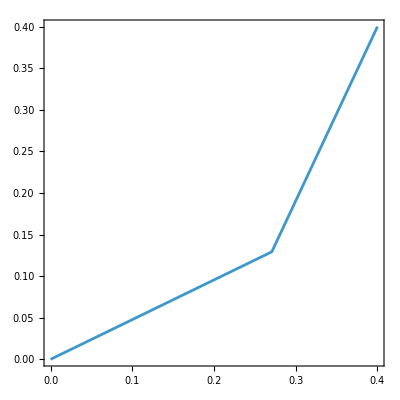

```mathematica
AN=N[A/.KinSol/.Data2];
PN=N[P/.KinSol/.Data2];
ListLinePlot[{{0,0},{AN⟦1⟧,AN⟦2⟧},{PN⟦1⟧,PN⟦2⟧}},Frame->True,AspectRatio->1]
```

If we need to produce a required orientation of the end effector (here π/4) we can only satisfy one of its coordinates (say, xd). Rotation of the end effector: EQI originated by RotBlock[[1,1]]==M03d[[1,1]] RotBlock[[1,2]]==M03d[[1,2]] Position xd and zd (EQII and EQIIII) of the end effector: EE[[1]]==xd EE[[3]]==zd. We still get two solutions:

```mathematica
Data3={L1->0.3,L2->0.3,h->1,xd->0.4,zd->0.4,ψd->Pi/4};
KinSol3=Solve[{RotBlock⟦1,1⟧ == M03d⟦1,1⟧,RotBlock⟦1,2⟧== M03d⟦1,2⟧,EE⟦1⟧ == xd,EE⟦3⟧ == zd}/. Data3,{θ1[t],θ2[t],L[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1[t]→-0.894093,θ2[t]→1.67949,L[t]→0.6},{θ1[t]→0.894093,θ2[t]→-0.108694,L[t]→0.6}}

If we produce the required orientation and xd coordinates of the end effector, we get two configurations . The first :

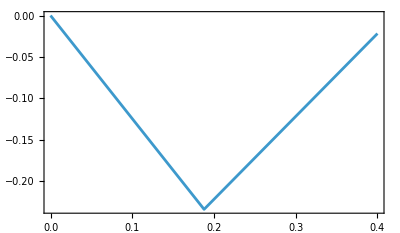

```mathematica
AN3=N[A/.KinSol3⟦1⟧/.Data3];
PN3=N[P/.KinSol3⟦1⟧/.Data3];
plot1=ListLinePlot[{{0,0},{AN3⟦1⟧,AN3⟦2⟧},{PN3⟦1⟧,PN3⟦2⟧}},Frame->True,AspectRatio->Automatic]
```

In this case, we are not fixing y. For this reason, if we plot the other solution of the system of equations, we get the same orientation but a different y position.

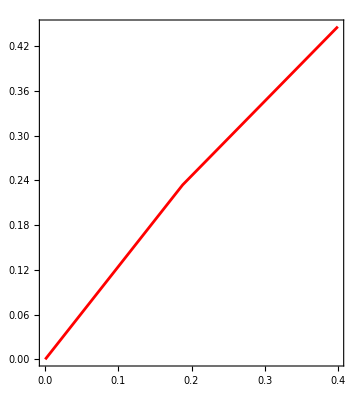

```mathematica
AN4=N[A/. KinSol3⟦2⟧/. Data3];
PN4=N[P/. KinSol3⟦2⟧/. Data3];
plot2=ListLinePlot[{{0,0},{AN4⟦1⟧,AN4⟦2⟧},{PN4⟦1⟧,PN4⟦2⟧}},PlotStyle->Red,Frame->True,AspectRatio->Automatic]
```

## 3. Force Ellipsoid

Force ellipsoids allow us to understand how costly it is, in terms of joint torques, to counteract forces applied to the end effector. In other words, how much force at the end-effector do I get for a torque unit at the joints. 
Let’s study the manipulability ellipsoids in the plane for the case of the Scara Robot in analysis. We restrict point E to the first two components (EEc) and perform the analysis.

```mathematica
EEc={EE⟦1⟧,EE⟦2⟧}/. θ1[t]->θ1/. θ2[t]->θ2;
EEc//MatrixForm (*The angles are no more function of time,so we substitute them to two variables*)
```

(L1 Cos[θ1]+L2 Cos[θ1+θ2]
L1 Sin[θ1]+L2 Sin[θ1+θ2])

Force ellipsoids comes from the computation of the kinetostatic of the manipulator. For this reason, the Jacobian is needed.

```mathematica
Jac=D[EEc,{{θ1,θ2}}];
Jac//MatrixForm(*Computing the Jacobian*)
```

(-L1 Sin[θ1]-L2 Sin[θ1+θ2] | -L2 Sin[θ1+θ2]
L1 Cos[θ1]+L2 Cos[θ1+θ2] | L2 Cos[θ1+θ2])

Check which are the singular configurations of the manipulator.

```mathematica
DetJac=Simplify[Det[Jac]](*Computing the determinant of the Jacobian*)
```

L1 L2 Sin[θ2]

```mathematica
θ1Singular=Simplify[Solve[Simplify[DetJac == 0],θ1]]
```

{}

I have no singular configurations for θ1 . It means that the first joint cannot generate a singular configuration .

```mathematica
θ2Singular=Simplify[Solve[DetJac == 0,θ2]] (*There are 2 singular configurations in θ2*)
```

{{θ2→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{θ2→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
Data={L1->0.3,L2->0.3, θ1->π/6,θ2->π/3};(*Robot data*)
```

```mathematica
A2={A⟦1⟧,A⟦2⟧}/. θ1[t]->θ1/. θ2[t]->θ2;
P2={P⟦1⟧,P⟦2⟧}/. θ1[t]->θ1/. θ2[t]->θ2;
```

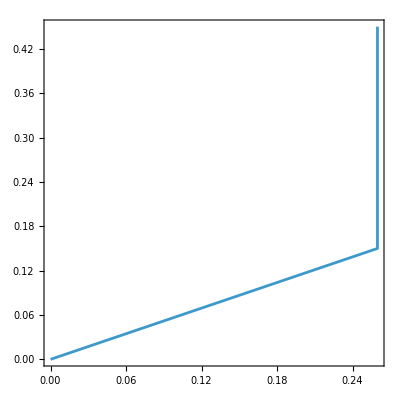

-Graphics-

```mathematica
AN2=N[A2/.Data];
PN2=N[P2/.Data];
ListLinePlot[{{0,0},AN2,PN2},Frame->True,AspectRatio->1]
```

```mathematica
F={Fx,Fy};(*External force components*)
```

```mathematica
FM=Simplify[Jac.Transpose[Jac]]; (*What is called A in the drawing*)
FM//MatrixForm (*Force ellipsoid matrix*)
```

(L2^2 Sin[θ1+θ2]^2+(L1 Sin[θ1]+L2 Sin[θ1+θ2])^2 | -L1^2 Cos[θ1] Sin[θ1]-L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])
-L1^2 Cos[θ1] Sin[θ1]-L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2]) | L2^2 Cos[θ1+θ2]^2+(L1 Cos[θ1]+L2 Cos[θ1+θ2])^2)

```mathematica
Fellipse=Simplify[Transpose[F].FM.F-Kf^2] (*Quadratic form of the Force ellipsoid*)
```

-Kf^2+Fy^2 L1^2 Cos[θ1]^2+2 Fy^2 L2^2 Cos[θ1+θ2]^2+Fx^2 L1^2 Sin[θ1]^2+2 Fy L1 Cos[θ1] (Fy L2 Cos[θ1+θ2]-Fx L1 Sin[θ1])+2 Fx^2 L1 L2 Sin[θ1] Sin[θ1+θ2]+2 Fx^2 L2^2 Sin[θ1+θ2]^2-2 Fx Fy L2^2 Sin[2 (θ1+θ2)]-2 Fx Fy L1 L2 Sin[2 θ1+θ2]

We can now compute a numerical expression for the force ellipsoid matrix

```mathematica
NumericalMatF=Simplify[FM/. Data/. {Kf->1}];
NumericalMatF//MatrixForm
```

(0.2925 | -0.116913
-0.116913 | 0.0675)

In order to visualize the ellipsoid and understand it' s meaning, we extract the eigenvalues and the eigenvector of the matrix .

```mathematica
EigVecF=Eigenvectors[NumericalMatF] 
EigVecF//MatrixForm (*Eigen vectors organized in ROWS*) 
EigValF=Eigenvalues[NumericalMatF] (*Eigen values sorted in decreasing absolute value*)
```

{{-0.920156,0.391551},{-0.391551,-0.920156}}

(-0.920156 | 0.391551
-0.391551 | -0.920156)

{0.34225,0.0177502}

If you need to extract the real part or you need to normalize you can use the following commands:

```mathematica
Re[EigValF⟦1⟧] (*RE command:extract real part of a complex number*)
```

0.34225

```mathematica
Norm[EigVecF⟦1⟧] 
Norm[EigVecF⟦2⟧](*Eigenvectors normalised to unitary norm*)
```

1.

1.

If we substitute now a value for the budget, we can now get the full expression of the force ellipsoid equation.

```mathematica
Fellipse/. Data/. {Kf->1}
```

-1.+0.2925 Fx^2+0.519615 (0.-0.15 Fx) Fy-0.155885 Fx Fy+0.0675 Fy^2

Let' s plot it

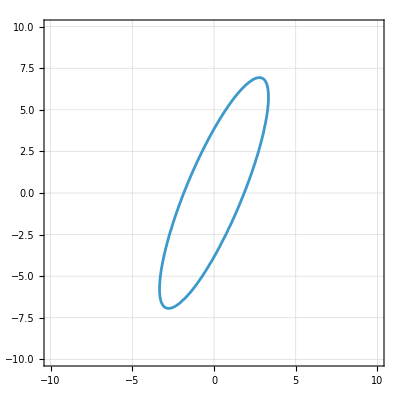

```mathematica
plContourF=ContourPlot[(Fellipse/. Data/. {Kf->1}) == 0,{Fx,-10,10},{Fy,-10,10},GridLines->Automatic]
```

In order to complete the figure, let’s plot also the eigenvector on it.

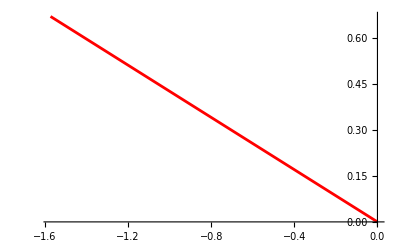

```mathematica
point1={0,0};point2=1/Sqrt[Re[EigValF⟦1⟧]] {Re[EigVecF⟦1,1⟧],Re[EigVecF⟦1,2⟧]};plEigVecF1=ListLinePlot[{point1,point2},PlotStyle->Red]
```

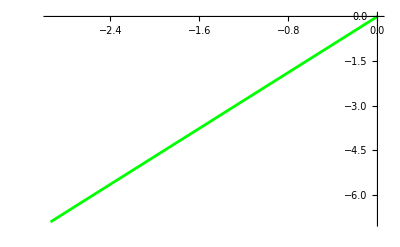

```mathematica
point3=1/Sqrt[Re[EigValF⟦2⟧]] {Re[EigVecF⟦2,1⟧],Re[EigVecF⟦2,2⟧]};plEigVecF2=ListLinePlot[{point1,point3},PlotStyle->Green]
```

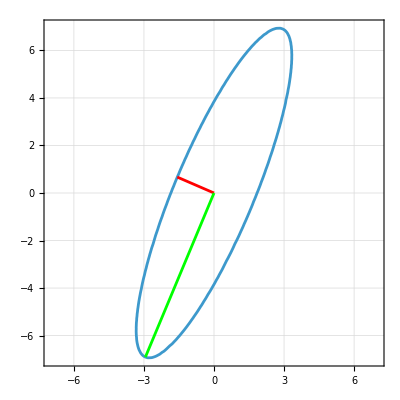

```mathematica
Show[{plContourF,plEigVecF1,plEigVecF2},PlotRange->{{-7,7},{-7,7}}] (*Plot the three figures together.*)
```

What is the maximum force applicable in a certain direction ? 
Let’s check the maximum force applicable along π/3

```mathematica
Fparam=s{Cos[π/3],Sin[π/3]}
```

{s/2,(√3 s)/2}

```mathematica
eqdir =  Simplify[Fellipse /. Data /. {Kf -> 1, Fx -> Fparam[[1]], Fy -> Fparam[[2]]}]
```

-1.+0.0225 s^2

Put this equation equal to 0 in order to identify s. I am basically finding the values of s such that my force is laying on the border of the ellipsoid. You can imagine the ellipsoid as the force region outside of which the robot cannot hold the applied force.

```mathematica
sintersect=Solve[eqdir == 0,s]
```

{{s→-6.66667},{s→6.66667}}

```mathematica
{Fmax1,Fmax2}=Fparam/. sintersect
```

{{-3.33333,-5.7735},{3.33333,5.7735}}

```mathematica
pointO={0,0};
pointF1=Fmax1;
pointF2=Fmax2;
plF1=ListLinePlot[{pointO,pointF1},PlotStyle->Red];
plF2=ListLinePlot[{pointO,pointF2},PlotStyle->Green];
```

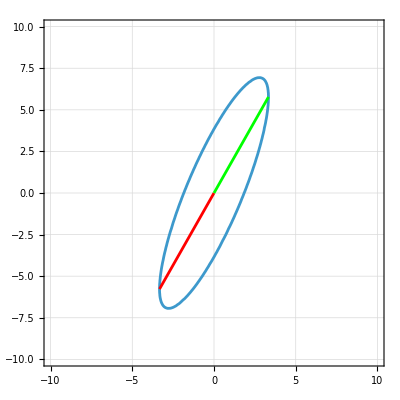

```mathematica
Show[{plContourF,plF1,plF2},PlotRange->{{-10,10},{-10,10}}]
```

As expected, the maximum force applicable in π/3 direction is touching the ellipsoid. The resulting forces are 2 because I can apply the same force but pulling or pushing the end effector in the same direction.

## 4. Velocity Ellipsoid

The velocity ellipsoid is representing the region of velocities that I can reach with the end effector and what is the cost related to each direction.  In other words, how much Cartesian speed I get at the end-effector for a unit of joint speed.

```mathematica
VM=Inverse[Jac.Transpose[Jac]]//Simplify;
VM//MatrixForm (*Velocity quadratic form matrix*)
```

(((L1^2 Cos[θ1]^2+2 L1 L2 Cos[θ1] Cos[θ1+θ2]+2 L2^2 Cos[θ1+θ2]^2) Csc[θ2]^2)/(L1^2 L2^2) | (Csc[θ2]^2 (L1^2 Cos[θ1] Sin[θ1]+L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])))/(L1^2 L2^2)
(Csc[θ2]^2 (L1^2 Cos[θ1] Sin[θ1]+L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])))/(L1^2 L2^2) | (Csc[θ2]^2 (L1^2 Sin[θ1]^2+2 L1 L2 Sin[θ1] Sin[θ1+θ2]+2 L2^2 Sin[θ1+θ2]^2))/(L1^2 L2^2))

```mathematica
V={Vx,Vy};(*Generic velocity array*)
```

```mathematica
Vellipse=FullSimplify[Transpose[V].VM.V-Kv^2] (*Velocity ellipsoid*)
```

-Kv^2+1/(L1^2 L2^2)Csc[θ2]^2 (L1^2 Vx^2 Cos[θ1]^2+2 L1 L2 Vx^2 Cos[θ1] Cos[θ1+θ2]+2 L2^2 Vx^2 Cos[θ1+θ2]^2+L1^2 Vy^2 Sin[θ1]^2+L1^2 Vx Vy Sin[2 θ1]+2 L2 Vy (L1 Vy Sin[θ1] Sin[θ1+θ2]+L2 Vy Sin[θ1+θ2]^2+L2 Vx Sin[2 (θ1+θ2)]+L1 Vx Sin[2 θ1+θ2]))

```mathematica
NumericalMatV=Simplify[VM/. Data/. {Kv->1}];
```

```mathematica
EigVecV=Eigenvectors[NumericalMatV];
EigVecV//MatrixForm(*Eigen vectors*) 
EigValV=Eigenvalues[NumericalMatV] (*Eigen values*)
```

(0.391551 | 0.920156
-0.920156 | 0.391551)

{56.3374,2.92184}

```mathematica
EigVecF//MatrixForm(*The eigenspaces of VM are the same as those of FM*) 
EigValF (*The eigenvalues of VM are the inverse of the eigenvalues of FM*)
```

(-0.920156 | 0.391551
-0.391551 | -0.920156)

{0.34225,0.0177502}

As before, let’s visualize the ellipsoid and the related eigenvectors.

```mathematica
point1={0,0};
point2=1/Sqrt[Re[EigValV[[1]]]] {Re[EigVecV[[1,1]]],Re[EigVecV[[1,2]]]};
plEigVecV1=ListLinePlot[{point1,point2},PlotStyle->Red];
```

```mathematica
point3=1/Sqrt[Re[EigValV[[2]]]] {Re[EigVecV[[2,1]]],Re[EigVecV[[2,2]]]};
plEigVecV2=ListLinePlot[{point1,point3},PlotStyle->Green];
```

```mathematica
plContourV=ContourPlot[(Vellipse/. Data/. {Kv->1}) == 0,{Vx,-1,1},{Vy,-1,1},GridLines->Automatic,ContourStyle->Cyan];
```

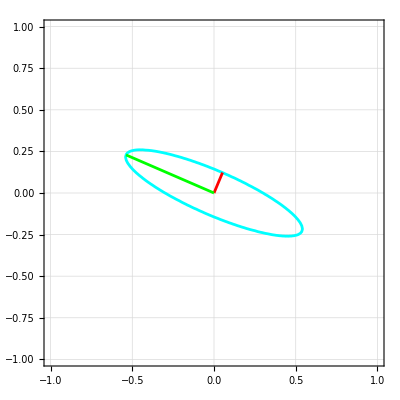

```mathematica
Show[{plContourV,plEigVecV1,plEigVecV2},PlotRange->{{-1,1},{-1,1}}]
```

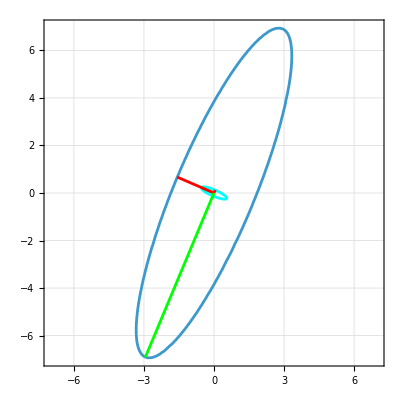

```mathematica
Show[{plContourV,plEigVecV1,plEigVecV2,plContourF,plEigVecF1,plEigVecF2},PlotRange->{{-7,7},{-7,7}}]
```

## 5. Compliance Ellipsoid

Compliance ellipsoid is representing a region of end-effector displacement for a unit of applied torque. In this sense, the longer the axis, the more displacement I get for a unit torque which translate in the joint being “soft” in that direction. In other words, how much Cartesian speed I get at the end-effector for a unit of force at the end-effector.

```mathematica
Kq=k*{{1,0},{0,2}};
Kq//MatrixForm (*Compliance matrix at the joint variables:dQ=-Kq.Fq*) 
Ks=Jac.Kq.Transpose[Jac]//FullSimplify;Ks//MatrixForm (*Compliance matrix at the absolute variables:dS=Js.Kq.JsT.Fs=Ks.Fs*) 
CM=Transpose[Inverse[Ks]].Inverse[Ks]//FullSimplify;CM//MatrixForm(*Compliace matrix at the absolute variables*)
```

(k | 0
0 | 2 k)

(k (2 L2^2 Sin[θ1+θ2]^2+(L1 Sin[θ1]+L2 Sin[θ1+θ2])^2) | -1/2 k (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2]))
-1/2 k (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2])) | k (2 L2^2 Cos[θ1+θ2]^2+(L1 Cos[θ1]+L2 Cos[θ1+θ2])^2))

((((L1^2+3 L2^2)^2+L1^2 (L1^2+5 L2^2) Cos[2 θ1]+L2 (L1^3 Cos[2 θ1-θ2]+4 L1 (L1^2+3 L2^2) Cos[θ2]+4 L1^2 L2 Cos[2 θ2]+5 L1^2 L2 Cos[2 (θ1+θ2)]+9 L2^3 Cos[2 (θ1+θ2)]+3 L1^3 Cos[2 θ1+θ2]+9 L1 L2^2 Cos[2 θ1+θ2]+3 L1 L2^2 Cos[2 θ1+3 θ2])) Csc[θ2]^4)/(8 k^2 L1^4 L2^4) | ((L1^2+3 L2^2+2 L1 L2 Cos[θ2]) Csc[θ2]^4 (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2])))/(8 k^2 L1^4 L2^4)
((L1^2+3 L2^2+2 L1 L2 Cos[θ2]) Csc[θ2]^4 (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2])))/(8 k^2 L1^4 L2^4) | -((-(L1^2+3 L2^2)^2+L1^2 (L1^2+5 L2^2) Cos[2 θ1]+L2 (L1^3 Cos[2 θ1-θ2]-4 L1 (L1^2+3 L2^2) Cos[θ2]-4 L1^2 L2 Cos[2 θ2]+5 L1^2 L2 Cos[2 (θ1+θ2)]+9 L2^3 Cos[2 (θ1+θ2)]+3 L1^3 Cos[2 θ1+θ2]+9 L1 L2^2 Cos[2 θ1+θ2]+3 L1 L2^2 Cos[2 θ1+3 θ2])) Csc[θ2]^4)/(8 k^2 L1^4 L2^4))

```mathematica
({{k, 0}, {0, 2 k}})
```

{{k,0},{0,2 k}}

```mathematica
dS={dx,dy};(*generic infinitesimal displacement*)
```

```mathematica
Cellipse=Simplify[Transpose[dS].CM.dS-KA^2] (*Compliance ellipsoid*)
```

1/(8 k^2 L1^4 L2^4)(-8 k^2 KA^2 L1^4 L2^4+dy^2 ((L1^2+3 L2^2)^2-L1^2 (L1^2+5 L2^2) Cos[2 θ1]-L2 (L1^3 Cos[2 θ1-θ2]-4 L1 (L1^2+3 L2^2) Cos[θ2]-4 L1^2 L2 Cos[2 θ2]+5 L1^2 L2 Cos[2 (θ1+θ2)]+9 L2^3 Cos[2 (θ1+θ2)]+3 L1^3 Cos[2 θ1+θ2]+9 L1 L2^2 Cos[2 θ1+θ2]+3 L1 L2^2 Cos[2 θ1+3 θ2])) Csc[θ2]^4+dx^2 ((L1^2+3 L2^2)^2+L1^2 (L1^2+5 L2^2) Cos[2 θ1]+L2 (L1^3 Cos[2 θ1-θ2]+4 L1 (L1^2+3 L2^2) Cos[θ2]+4 L1^2 L2 Cos[2 θ2]+5 L1^2 L2 Cos[2 (θ1+θ2)]+9 L2^3 Cos[2 (θ1+θ2)]+3 L1^3 Cos[2 θ1+θ2]+9 L1 L2^2 Cos[2 θ1+θ2]+3 L1 L2^2 Cos[2 θ1+3 θ2])) Csc[θ2]^4+2 dx dy (L1^2+3 L2^2+2 L1 L2 Cos[θ2]) Csc[θ2]^4 (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2])))

```mathematica
NumericalMatC=Simplify[CM/. Data/. {KA->1,k->1}];NumericalMatC//MatrixForm
```

(123.457 | 356.389
356.389 | 1083.68)

```mathematica
EigVecC=Eigenvectors[NumericalMatC];
EigVecC//MatrixForm (*Eigen vectors*) 
EigValC=Eigenvalues[NumericalMatC] (*Eigen values*)
EigValF
```

(0.313883 | 0.949462
-0.949462 | 0.313883)

{1201.5,5.63801}

{0.34225,0.0177502}

```mathematica
point1={0,0};point2=1/Sqrt[Re[EigValC[[1]]]] {Re[EigVecC[[1,1]]],Re[EigVecC[[1,2]]]};plEigVecC1=ListLinePlot[{point1,point2},PlotStyle->Red];point3=1/Sqrt[Re[EigValC[[2]]]] {Re[EigVecC[[2,1]]],Re[EigVecC[[2,2]]]};plEigVecC2=ListLinePlot[{point1,point3},PlotStyle->Green];
```

```mathematica
plContourC=ContourPlot[(Cellipse/. Data/. {KA->1,k->1}) == 0,{dx,-0.7,0.7},{dy,-0.7,0.7},GridLines->Automatic,ContourStyle->Black];
```

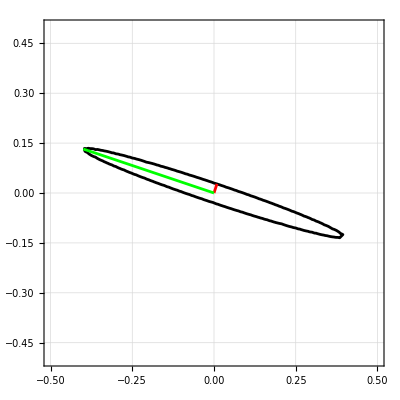

```mathematica
Show[{plContourC,plEigVecC1,plEigVecC2},PlotRange->{{-0.5,0.5},{-0.5,0.5}}]
```

## 6. Velocity Analysis: Direct Kinematics

Velocity analysis using direct kinematics is the process of determining the linear and angular velocities of the robot’s end-effector (and possibly of intermediate links) as a function of the joint velocities, by differentiating the direct kinematic model. Velocities can be relative or absolute wrt the reference frame they are expressed into.  We want to compute the absolute velocity of the end-effector. 
We start by computing the velocity of point A wrt frame 0.

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm (*Velocity matrix of reference frame 1 wrt 0 of generic a unitary point *)
```

(0 | -θ1'[t] | 0 | 0
θ1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

This solution can be obtained using elicoidal transformations. The following elicoidal transformation is specific for a rotation without translation around z.

```mathematica
Lrot={{0,-1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}; (*Generic elicoidal matrix representing a rotation around z*)
L01=Lrot;L01//MatrixForm 
L01*D[θ1[t],t]//MatrixForm (*The product by the joint velocity gives the velocity matrix*)
```

(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -θ1'[t] | 0 | 0
θ1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Velocity of point A wrt reference frame 0  is obtained by multiplying the coordinates of the point projected in 0 by the relative velocity matrix.

```mathematica
A={L1*Cos[θ1[t]],L1*Sin[θ1[t]],h,1};(*PointAw.r.t.RF0*)
```

```mathematica
W01.A//MatrixForm
```

(-L1 Sin[θ1[t]] θ1'[t]
L1 Cos[θ1[t]] θ1'[t]
0
0)

We go on by finding relative velocity of point P body-fixed to frame 2 with respect to frame 1, projected in frame 1. To do this, we have to find the relative velocity matrix of frame 2 wrt frame 1, expressed in frame 1 (“F1”).

```mathematica
W12F1=Simplify[D[M12,t].Inverse[M12]];
W12F1//MatrixForm
```

(0 | -θ2'[t] | 0 | 0
θ2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12F1.P1//MatrixForm
```

(-L2 Sin[θ2[t]] θ2'[t]
L2 Cos[θ2[t]] θ2'[t]
0
0)

To express the relative velocity of point P projected in frame 0, the velocity matrix W12F1 has to be expressed in frame 0.

-Graphics-

```mathematica
W12=Simplify[M01.W12F1.Inverse[M01]];
W12//MatrixForm
```

(0 | -θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Simplify[W12.P]//MatrixForm
```

(-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
L2 Cos[θ1[t]+θ2[t]] θ2'[t]
0
0)

Again, we could obtain the same result by using elicoidal transformations

```mathematica
L12F1=Lrot; (*Elicoidal transf of ref2 wrt ref1 projected in ref1*)
```

The product by the joint velocity gives the velocity matrix W12F1

```mathematica
L12F1* D[θ2[t],t]//MatrixForm
```

(0 | -θ2'[t] | 0 | 0
θ2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

If we want to express this in reference frame 0, the idea is the same as before.

```mathematica
L12=Simplify[M01.L12F1.Inverse[M01]];
L12 // MatrixForm

L12* D[θ2[t],t]//MatrixForm
```

(0 | -1 | 0 | L1 Sin[θ1[t]]
1 | 0 | 0 | -L1 Cos[θ1[t]]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

This result is indicating that the velocity of reference frame 2 wrt reference frame has no influence on the velocity of reference frame 1, as expected. In other words, the velocity of point A produced by the joint from link 1 to 2 is zero.

```mathematica
Simplify[W12.A]//MatrixForm
```

(0
0
0
0)

If we want calculate absolute velocities it means that we want to express velocities of local reference frames wrt the absolute reference frames and projecting them in the absolute reference frame . To do this, we can make use of the Rival' s Theorem . Let' s use it to compute the absolute velocity of point P .
  
  -Graphics-

```mathematica
W02=Simplify[W01+W12];W02//MatrixForm (*Absolute velocity matrix of link 2*)
```

(0 | -θ1'[t]-θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ1'[t]+θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Simplify[W02.P]//MatrixForm (*Absolute velocity of point P *)
```

(-((L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t])-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
0
0)

Let’s complete the analysis by calculating the velocity of the end effector. 
Start by considering  the velocity matrix of link 3 produced only by the joint between 2 and 3, expressed in frame 2

```mathematica
W23F2=D[M23,t].Inverse[M23];W23F2//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

The same matrix expressed in frame 0

```mathematica
W23=M02.W23F2.Inverse[M02];W23//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

Considering that now we are using a prismatic joint, the relative elicoidal trasnformation matrix is different.

```mathematica
Ltraslz={{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}};Ltraslz//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

This is generic. For our specific case,m the translation is happening along -z.

```mathematica
L23F2=-Ltraslz;
```

```mathematica
W23F2=L23F2*D[L[t],t];W23F2//MatrixForm (*the product with the joint velocity gives the velocity matrix*)
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

In reference frame 0:

```mathematica
L23=M02.L23F2.Inverse[M02];L23//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 0 | 0)

Finally, let’s compute the absolute velocity of the end effector.

```mathematica
W03=W01+W12+W23;W03//MatrixForm
```

(0 | -θ1'[t]-θ2'[t] | 0 | L1 Sin[θ1[t]] θ2'[t]
θ1'[t]+θ2'[t] | 0 | 0 | -L1 Cos[θ1[t]] θ2'[t]
0 | 0 | 0 | -L'[t]
0 | 0 | 0 | 0)

```mathematica
VE=Simplify[W03.EE];VE//MatrixForm
```

(-((L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t])-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
-L'[t]
0)

```mathematica
UnitVel={D[θ1[t],t]->1,D[θ2[t],t]->1,D[L[t],t]->1};
```

```mathematica
Data = {L1->0.3,L2->0.3, h->1};
VE/. KinSol/. Data/. UnitVel
```

{-0.670711,0.529289,-1,0}

## 7. Velocity Analysis: Inverse Kinematics

The inverse kinematic problem finds the joint velocities required to produce a given velocity matrix of the end effector (link 3) . The end effector is described by the coordinates of point E and the rotation about the vertical axis . In the inverse kinematics we want to find the joint velocities required to produce a given velocity configuration of the end effector. As for the inverse kinematics problem for the position and orientation of the end effector, the set of equations will be over-costrained and we’ll be able to satisfy only 3 out of the 4 desired variables (cartesian velocisities of the end-effector and angular velocity in z).

```mathematica
VE // MatrixForm
```

(-((L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t])-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
-L'[t]
0)

```mathematica
vars={D[θ1[t],t],D[θ2[t],t],D[L[t],t]};
vars//MatrixForm
```

(θ1'[t]
θ2'[t]
L'[t])

```mathematica
invproblem=Simplify[Solve[{VE⟦1⟧ == VX,VE⟦2⟧ == VY,VE⟦3⟧ == VZ},vars]];
invproblem//MatrixForm (*Analytical Solution*)
```

(θ1'[t]→(Csc[θ2[t]] (VX Cos[θ1[t]+θ2[t]]+VY Sin[θ1[t]+θ2[t]]))/L1 | θ2'[t]→-(Csc[θ2[t]] (L1 VX Cos[θ1[t]]+L2 VX Cos[θ1[t]+θ2[t]]+L1 VY Sin[θ1[t]]+L2 VY Sin[θ1[t]+θ2[t]]))/(L1 L2) | L'[t]→-VZ)

Set the desired cartesian velocity at the end-effector in order to get a numerical solution for the joint velocities

```mathematica
invproblem⟦1,1⟧/. {VX->1,VY->1,VZ->1}/. Data/. KinSol
invproblem⟦1,2⟧/. {VX->1,VY->1,VZ->1}/. Data/. KinSol
invproblem⟦1,3⟧/. {VX->1,VY->1,VZ->1}/. Data/. KinSol
```

θ1'[t]→7.07107

θ2'[t]→-14.1421

L'[t]→-1

Let’s try now to get to the same solution with a different approach. We set a linear problem.
We start by defining the implicit equations.

```mathematica
eqs=Simplify[{VE⟦1⟧-VX,VE⟦2⟧-VY,VE⟦3⟧-VZ,W03⟦1,2⟧-(-ωz)}];
eqs//MatrixForm
```

(-VX-(L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) θ1'[t]-L2 Sin[θ1[t]+θ2[t]] θ2'[t]
-VY+(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) θ1'[t]+L2 Cos[θ1[t]+θ2[t]] θ2'[t]
-VZ-L'[t]
ωz-θ1'[t]-θ2'[t])

Extract the coefficients in order to get into a linear form.

```mathematica
Jac=Normal[CoefficientArrays[eqs,vars]]⟦2⟧;
Jac // MatrixForm
```

(-L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]] | -L2 Sin[θ1[t]+θ2[t]] | 0
L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]] | L2 Cos[θ1[t]+θ2[t]] | 0
0 | 0 | -1
-1 | -1 | 0)

```mathematica
CoefficientArrays[eqs,vars][[1]]//MatrixForm
```

(-VX
-VY
-VZ
ωz)

```mathematica
(Jac//MatrixForm).(vars//MatrixForm) == MatrixForm[{VX,VY,VZ,ωz}]
```

(-L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]] | -L2 Sin[θ1[t]+θ2[t]] | 0
L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]] | L2 Cos[θ1[t]+θ2[t]] | 0
0 | 0 | -1
-1 | -1 | 0).(θ1'[t]
θ2'[t]
L'[t])==(VX
VY
VZ
ωz)

```mathematica
Jac/.KinSol/.Data // MatrixForm
```

(-0.4 | -0.270711 | 0
0.4 | 0.129289 | 0
0 | 0 | -1
-1 | -1 | 0)

We have to discard one of the equations. We discard the angular rate of frame 3 and, consequently, we set just the cartesian velocities for the end-effector.

```mathematica
RotJac=Jac⟦1;;3,;;⟧;RotJac//MatrixForm
```

(-L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]] | -L2 Sin[θ1[t]+θ2[t]] | 0
L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]] | L2 Cos[θ1[t]+θ2[t]] | 0
0 | 0 | -1)

The linear

```mathematica
(RotJac//MatrixForm).(vars//MatrixForm) == MatrixForm[{VX,VY,VZ}]
```

(-L1 Sin[θ1[t]]-L2 Sin[θ1[t]+θ2[t]] | -L2 Sin[θ1[t]+θ2[t]] | 0
L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]] | L2 Cos[θ1[t]+θ2[t]] | 0
0 | 0 | -1).(θ1'[t]
θ2'[t]
L'[t])==(VX
VY
VZ)

```mathematica
jointvel=Simplify[Inverse[RotJac]].{VX,VY,VZ};jointvel//MatrixForm (*These are the expressions for: θ1dot, θ2dot, Ldot*)
```

((VX Cos[θ1[t]+θ2[t]] Csc[θ2[t]])/L1+(VY Csc[θ2[t]] Sin[θ1[t]+θ2[t]])/L1
-(VX (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) Csc[θ2[t]])/(L1 L2)-(VY Csc[θ2[t]] (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]))/(L1 L2)
-VZ)

```mathematica
N[jointvel]/. {VX->1,VY->1,VZ->1,L1->0.3,L2->0.3,h->1}/. KinSol (*Substitute to the symbolic expression the desired joint velocities*)
```

{7.07107,-14.1421,-1.}

## 8. Dynamics

-Graphics-

In order to obtain the equations of motion, which are going to be 3 (3 independent variables), let’s start by defining the Lagrangian term.

```mathematica
J11={{1/3*L1^3*ρ1,0,0,-m1*L1/2},{0,0,0,0},{0,0,0,0},{-m1*L1/2,0,0,m1}}; (*Inertia tensor of mass1 wrt ref1*)
J11//MatrixForm
```

((L1^3 ρ1)/3 | 0 | 0 | -(L1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(L1 m1)/2 | 0 | 0 | m1)

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];(*Inertia tensor of mass1 wrt ref0*)
J10//MatrixForm
```

(1/3 L1^3 ρ1 Cos[θ1[t]]^2 | 1/6 L1^3 ρ1 Sin[2 θ1[t]] | 1/2 h L1 m1 Cos[θ1[t]] | 1/2 L1 m1 Cos[θ1[t]]
1/6 L1^3 ρ1 Sin[2 θ1[t]] | 1/3 L1^3 ρ1 Sin[θ1[t]]^2 | 1/2 h L1 m1 Sin[θ1[t]] | 1/2 L1 m1 Sin[θ1[t]]
1/2 h L1 m1 Cos[θ1[t]] | 1/2 h L1 m1 Sin[θ1[t]] | h^2 m1 | h m1
1/2 L1 m1 Cos[θ1[t]] | 1/2 L1 m1 Sin[θ1[t]] | h m1 | m1)

```mathematica
T1=Simplify[Tr[1/2W01.J10.Transpose[W01]]](*Kinematic Energy of mass1*)
```

1/6 L1^3 ρ1 θ1'[t]^2

```mathematica
J22={{1/3*L2^3*ρ2,0,0,-m2*L2/2},{0,0,0,0},{0,0,0,0},{-m2*L2/2,0,0,m2}};(*Inertia tensor of mass2 wrt ref2*)
J22//MatrixForm 
J20=Simplify[M02.J22.Transpose[M02]] (*Inertia tensor of mass2 wrt ref0*)
T2=Simplify[Tr[1/2W02.J20.Transpose[W02]]]
```

((L2^3 ρ2)/3 | 0 | 0 | -(L2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(L2 m2)/2 | 0 | 0 | m2)

{{L1^2 m2 Cos[θ1[t]]^2+L1 L2 m2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]]+1/3 L2^3 ρ2 Cos[θ1[t]+θ2[t]]^2,1/6 (3 L1^2 m2 Sin[2 θ1[t]]+L2^3 ρ2 Sin[2 (θ1[t]+θ2[t])]+3 L1 L2 m2 Sin[2 θ1[t]+θ2[t]]),1/2 h m2 (2 L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]),L1 m2 Cos[θ1[t]]+1/2 L2 m2 Cos[θ1[t]+θ2[t]]},{1/6 (3 L1^2 m2 Sin[2 θ1[t]]+L2^3 ρ2 Sin[2 (θ1[t]+θ2[t])]+3 L1 L2 m2 Sin[2 θ1[t]+θ2[t]]),L1^2 m2 Sin[θ1[t]]^2+L1 L2 m2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]]+1/3 L2^3 ρ2 Sin[θ1[t]+θ2[t]]^2,1/2 h m2 (2 L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),L1 m2 Sin[θ1[t]]+1/2 L2 m2 Sin[θ1[t]+θ2[t]]},{1/2 h m2 (2 L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]),1/2 h m2 (2 L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),h^2 m2,h m2},{L1 m2 Cos[θ1[t]]+1/2 L2 m2 Cos[θ1[t]+θ2[t]],L1 m2 Sin[θ1[t]]+1/2 L2 m2 Sin[θ1[t]+θ2[t]],h m2,m2}}

1/6 ((3 L1^2 m2+L2^3 ρ2+3 L1 L2 m2 Cos[θ2[t]]) θ1'[t]^2+L2 (2 L2^2 ρ2+3 L1 m2 Cos[θ2[t]]) θ1'[t] θ2'[t]+L2^3 ρ2 θ2'[t]^2)

```mathematica
J33={{0,0,0,0},{0,0,0,0},{0,0,1/3*L3^3*ρ3,m3*L3/2},{0,0,m3*L3/2,m3}};(*Inertia tensor of mass3 wrt ref3*)
J33//MatrixForm 
J30=Simplify[M03.J33.Transpose[M03]](*Inertia tensor of mass3 wrt ref0*)
T3=Simplify[Tr[1/2W03.J30.Transpose[W03]]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (L3^3 ρ3)/3 | (L3 m3)/2
0 | 0 | (L3 m3)/2 | m3)

{{m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]])^2,m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),1/2 m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) (2 h+L3-2 L[t]),m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]])},{m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),m3 (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]])^2,1/2 m3 (2 h+L3-2 L[t]) (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),m3 (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]])},{1/2 m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) (2 h+L3-2 L[t]),1/2 m3 (2 h+L3-2 L[t]) (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),h^2 m3+h L3 m3+(L3^3 ρ3)/3-(2 h+L3) m3 L[t]+m3 L[t]^2,1/2 m3 (2 h+L3-2 L[t])},{m3 (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]),m3 (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]),1/2 m3 (2 h+L3-2 L[t]),m3}}

1/2 m3 (L'[t]^2+(L1^2+L2^2+2 L1 L2 Cos[θ2[t]]) θ1'[t]^2+2 L2 (L2+L1 Cos[θ2[t]]) θ1'[t] θ2'[t]+L2^2 θ2'[t]^2)

```mathematica
Hg1={{0,0,0,0},{0,0,0,0},{0,0,0,-g},{0,0,0,0}};
Hg1//MatrixForm 
Hg2=Hg1;Hg3=Hg1;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -g
0 | 0 | 0 | 0)

```mathematica
Ug1=Tr[-Hg1.J10] 
Ug2=Tr[-Hg1.J20] 
Ug3=Tr[-Hg1.J30]
```

g h m1

g h m2

1/2 g m3 (2 h+L3-2 L[t])

```mathematica
Lagr=FullSimplify[T1+T2+T3-Ug1-Ug2-Ug3]
```

1/6 (-6 g h (m1+m2)-3 g (2 h+L3) m3+6 g m3 L[t]+3 m3 L'[t]^2+(3 L1^2 (m2+m3)+L1^3 ρ1+L2^2 (3 m3+L2 ρ2)+3 L1 L2 (m2+2 m3) Cos[θ2[t]]) θ1'[t]^2+L2 (2 L2 (3 m3+L2 ρ2)+3 L1 (m2+2 m3) Cos[θ2[t]]) θ1'[t] θ2'[t]+L2^2 (3 m3+L2 ρ2) θ2'[t]^2)

Left Hand Side Eq. Motion 1

```mathematica
dLagrdθ1dotdt=D[D[Lagr,θ1'[t]],t]
```

1/6 (-6 L1 L2 (m2+2 m3) Sin[θ2[t]] θ1'[t] θ2'[t]-3 L1 L2 (m2+2 m3) Sin[θ2[t]] θ2'[t]^2+2 (3 L1^2 (m2+m3)+L1^3 ρ1+L2^2 (3 m3+L2 ρ2)+3 L1 L2 (m2+2 m3) Cos[θ2[t]]) θ1''[t]+L2 (2 L2 (3 m3+L2 ρ2)+3 L1 (m2+2 m3) Cos[θ2[t]]) θ2''[t])

```mathematica
dLagrdθ1=D[Lagr,θ1[t]]
```

0

Left Hand Side Eq . Motion 2

```mathematica
dLagrdθ2dotdt=D[D[Lagr,θ2'[t]],t]
```

1/6 (-3 L1 L2 (m2+2 m3) Sin[θ2[t]] θ1'[t] θ2'[t]+L2 (2 L2 (3 m3+L2 ρ2)+3 L1 (m2+2 m3) Cos[θ2[t]]) θ1''[t]+2 L2^2 (3 m3+L2 ρ2) θ2''[t])

```mathematica
dLagrdθ2=D[Lagr,θ2[t]]
```

1/6 (-3 L1 L2 (m2+2 m3) Sin[θ2[t]] θ1'[t]^2-3 L1 L2 (m2+2 m3) Sin[θ2[t]] θ1'[t] θ2'[t])

Left Hand Side Eq . Motion 3

```mathematica
dLagrdLdotdt=D[D[Lagr,L'[t]],t]
```

m3 L''[t]

```mathematica
dLagrdL=D[Lagr,L[t]]
```

g m3

At this point, we just miss the non-lagrangian components for the 3 equations. 
Let’s compute the action matrix

```mathematica
Phi11={{0,-Cθ1+Cθ2,0,0},{+Cθ1-Cθ2,0,0,0},{0,0,0,0},{0,0,0,0}};(*matrix of actions on link1 wrt  ref1*)
Phi11//MatrixForm
```

(0 | -Cθ1+Cθ2 | 0 | 0
Cθ1-Cθ2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Phi1=Simplify[M01.Phi11.Transpose[M01]];
Phi1//MatrixForm
```

(0 | -Cθ1+Cθ2 | 0 | 0
Cθ1-Cθ2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[F]
```

```mathematica
Phi22={{0,-Cθ2,0,0},{+Cθ2,0,0,0},{0,0,0,F},{0,0,-F,0}};Phi22//MatrixForm
```

(0 | -Cθ2 | 0 | 0
Cθ2 | 0 | 0 | 0
0 | 0 | 0 | F
0 | 0 | -F | 0)

```mathematica
Phi2=Simplify[M02.Phi22.Transpose[M02]];
Phi2//MatrixForm
```

(0 | -Cθ2 | -F (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) | 0
Cθ2 | 0 | -F (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) | 0
F (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) | F (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) | 0 | F
0 | 0 | -F | 0)

```mathematica
Phi33={{0,0,0,0},{0,0,0,0},{0,0,0,-F},{0,0,F,0}};Phi33//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -F
0 | 0 | F | 0)

```mathematica
Phi3=Simplify[M03.Phi33.Transpose[M03]];
Phi3//MatrixForm
```

(0 | 0 | F (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) | 0
0 | 0 | F (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) | 0
-F (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]) | -F (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) | 0 | -F
0 | 0 | F | 0)

It is convenient to define external actions in an auxiliary reference system that has axis parallel to the base frame but origin in the EE

```mathematica
Phi3ea3={{0,-CE,0,Fx},{CE,0,0,Fy},{0,0,0,Fz},{-Fx,-Fy,-Fz,0}};Phi3ea3//MatrixForm
```

(0 | -CE | 0 | Fx
CE | 0 | 0 | Fy
0 | 0 | 0 | Fz
-Fx | -Fy | -Fz | 0)

```mathematica
M0a3=Mrotztrasl[0,EE];
M0a3//MatrixForm
```

(1 | 0 | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
0 | 1 | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
Phi3e=Simplify[M0a3.Phi3ea3.Transpose[M0a3]];
Phi3e//MatrixForm
```

(0 | -CE-Fy L1 Cos[θ1[t]]-Fy L2 Cos[θ1[t]+θ2[t]]+Fx L1 Sin[θ1[t]]+Fx L2 Sin[θ1[t]+θ2[t]] | -Fz (L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]])+Fx (h-L[t]) | Fx
CE+Fy L1 Cos[θ1[t]]+Fy L2 Cos[θ1[t]+θ2[t]]-Fx L1 Sin[θ1[t]]-Fx L2 Sin[θ1[t]+θ2[t]] | 0 | Fy (h-L[t])-Fz (L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]) | Fy
-Fx h+Fz L1 Cos[θ1[t]]+Fz L2 Cos[θ1[t]+θ2[t]]+Fx L[t] | -Fy h+Fy L[t]+Fz L1 Sin[θ1[t]]+Fz L2 Sin[θ1[t]+θ2[t]] | 0 | Fz
-Fx | -Fy | -Fz | 0)

To get to the expression of the non-Lagrangian components of forces and torques, we can use the general formula for serial robots.

```mathematica
PSP[matrix1_,matrix2_]:=matrix1⟦3,2⟧×matrix2⟦3,2⟧+matrix1⟦1,3⟧×matrix2⟦1,3⟧+matrix1⟦2,1⟧×matrix2⟦2,1⟧+matrix1⟦1,4⟧×matrix2⟦1,4⟧+matrix1⟦2,4⟧×matrix2⟦2,4⟧+matrix1⟦3,4⟧×matrix2⟦3,4⟧;
```

```mathematica
Q1=Simplify[PSP[Phi1+Phi2+Phi3+Phi3e,W01]/D[θ1'[t]]]
```

CE+Cθ1+Fy L1 Cos[θ1[t]]+Fy L2 Cos[θ1[t]+θ2[t]]-Fx L1 Sin[θ1[t]]-Fx L2 Sin[θ1[t]+θ2[t]]

```mathematica
Q1=Simplify[PSP[Phi1+Phi2+Phi3+Phi3e,L01]](*You can get to the same result if you use L01*)
```

CE+Cθ1+Fy L1 Cos[θ1[t]]+Fy L2 Cos[θ1[t]+θ2[t]]-Fx L1 Sin[θ1[t]]-Fx L2 Sin[θ1[t]+θ2[t]]

```mathematica
Q2=Simplify[PSP[Phi2+Phi3+Phi3e,L12]]
```

CE+Cθ2+Fy L2 Cos[θ1[t]+θ2[t]]-Fx L2 Sin[θ1[t]+θ2[t]]

```mathematica
Q3=Simplify[PSP[Phi3+Phi3e,L23]]
```

F-Fz

```mathematica
equation1=dLagrdθ1dotdt-dLagrdθ1-Q1//Simplify 
equation2=dLagrdθ2dotdt-dLagrdθ2-Q2//Simplify 
equation3=dLagrdLdotdt-dLagrdL-Q3//Simplify
```

-CE-Cθ1-Fy L1 Cos[θ1[t]]-Fy L2 Cos[θ1[t]+θ2[t]]+Fx L1 Sin[θ1[t]]+Fx L2 Sin[θ1[t]+θ2[t]]+1/6 (-6 L1 L2 (m2+2 m3) Sin[θ2[t]] θ1'[t] θ2'[t]-3 L1 L2 (m2+2 m3) Sin[θ2[t]] θ2'[t]^2+2 (3 L1^2 (m2+m3)+L1^3 ρ1+L2^2 (3 m3+L2 ρ2)+3 L1 L2 (m2+2 m3) Cos[θ2[t]]) θ1''[t]+L2 (2 L2 (3 m3+L2 ρ2)+3 L1 (m2+2 m3) Cos[θ2[t]]) θ2''[t])

1/6 (-6 CE-6 Cθ2-6 Fy L2 Cos[θ1[t]+θ2[t]]+6 Fx L2 Sin[θ1[t]+θ2[t]]+3 L1 L2 (m2+2 m3) Sin[θ2[t]] θ1'[t]^2+L2 (2 L2 (3 m3+L2 ρ2)+3 L1 (m2+2 m3) Cos[θ2[t]]) θ1''[t]+6 L2^2 m3 θ2''[t]+2 L2^3 ρ2 θ2''[t])

-F+Fz-g m3+m3 L''[t]

For this case of study we use a simplification : L (t) = const . In this way, equation 3 becomes a static equilibrium, uncoupled from the other two equations.

```mathematica
equation3/. L''[t]->0
```

-F+Fz-g m3

## 9. Direct Dynamics

```mathematica
data={L1->0.3,L2->0.3,L3->0.3,m1->15,m2->8,m3->6,ρ1->15/0.3,ρ2->8/0.3,ρ3->6/0.3};
```

Now, given a certain external force, we check how the system responds.This is called Direct Dynamics. Here we assume that the only acting force is the one in x direction.

```mathematica
actions={CE->0,Fx->10,Fy->0,Fz->0}; (*We are assuming that the EE is touching an object and generate a reaction only along x*)
```

```mathematica
e1b=Simplify[equation1/. Union[data,actions,{Cθ1->0}]] 
e2b=Simplify[equation2/. Union[data,actions,{Cθ2->0}]]
```

3. Sin[θ1[t]]+3. Sin[θ1[t]+θ2[t]]-1.8 Sin[θ2[t]] θ1'[t] θ2'[t]-0.9 Sin[θ2[t]] θ2'[t]^2+2.49 θ1''[t]+1.8 Cos[θ2[t]] θ1''[t]+0.78 θ2''[t]+0.9 Cos[θ2[t]] θ2''[t]

3. Sin[θ1[t]+θ2[t]]+0.9 Sin[θ2[t]] θ1'[t]^2+(0.78+0.9 Cos[θ2[t]]) θ1''[t]+0.78 θ2''[t]

```mathematica
tend=20;
ds1=Flatten@NDSolve[{e1b == 0,e2b ==0,θ1[0] ==0,θ1'[0] == 0,θ2[0] == π/6,θ2'[0] == 0},{θ1[t],θ2[t]},{t,0,tend}]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

```mathematica
θ1t=θ1[t]/. ds1 
θ2t=θ2[t]/. ds1
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

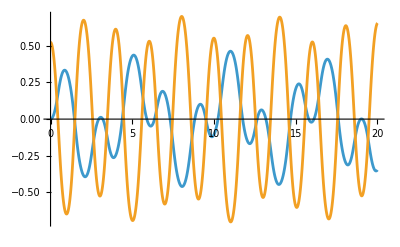

```mathematica
Plot[{θ1t,θ2t},{t,0,20}]
```

```mathematica
θ1dot=D[θ1t,t] 
θ2dot=D[θ2t,t]
```

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

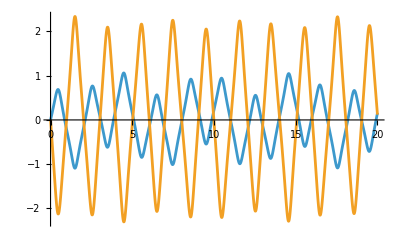

```mathematica
Plot[{θ1dot,θ2dot},{t,0,20}]
```

## 10. Inverse Dynamics

A repositioning from zero joint coordinates to the solution “KinSol” (xd->0.4,yd->0.4,zd->0.4) is happening  in T = 2 s.  We want to move between this two points with a profile compose of 2 different parts. Until T/2 I want to move with  constant acceleration and then move with constant deceleration.  The initial and final velocities are zero. The value for the acceleration is the same, we just change the sign. The maximum possible acceleration that I can apply is coming from the following expression.

```mathematica
Flatten[Solve[qf-qi== 1/2 *a*T^2,a]]
```

{a→(2 (qf-qi))/T^2}

The motion profile is describe as a piecewise. Until T/2 I move with positive acceleration and then it becomes negative

```mathematica
baseProfile=Piecewise[{{0,t<0},{qin+2*(qfin-qin)(t/T)^2,0<=t<=T/2},{qfin-1/2*4(qfin-qin)(t-T)^2/T^2,T/2<t<=T},{qfin,t>T}}]
```

Piecewise[{{0, t<0}, {qin+(2 (qfin-qin) t^2)/T^2, 0≤t≤T/2}, {qfin-(2 (qfin-qin) (t-T)^2)/T^2, T/2<t≤T}, {qfin, t>T}, {0, True}}]

```mathematica
prof1=baseProfile/.{qin->0,qfin->(θ1[t]/.KinSol),T->2} 
prof2=baseProfile/.{qin->0,qfin->(θ2[t]/.KinSol),T->2}
prof3=baseProfile/.{qin->0,qfin->(L[t]/.KinSol),T->2}
```

Piecewise[{{0, t<0}, {0.222781 t^2, 0≤t≤1}, {0.445561-0.222781 (-2+t)^2, 1<t≤2}, {0.445561, t>2}, {0, True}}]

Piecewise[{{0, t<0}, {0.339837 t^2, 0≤t≤1}, {0.679674-0.339837 (-2+t)^2, 1<t≤2}, {0.679674, t>2}, {0, True}}]

Piecewise[{{0, t<0}, {0.3 t^2, 0≤t≤1}, {0.6-0.3 (-2+t)^2, 1<t≤2}, {0.6, t>2}, {0, True}}]

The corresponding profiles for the 3 independent variables is as follow

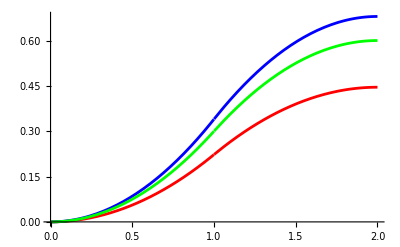

```mathematica
pl1=Plot[prof1,{t,0,2},PlotRange->All,PlotStyle->Red];
pl2=Plot[prof2,{t,0,2},PlotStyle->Blue];
pl3=Plot[prof3,{t,0,2},PlotStyle->Green];
Show[{pl1,pl2,pl3}]
```

Now, we can compute the inverse dynamics by substituting the motion profiles to our external actions.

```mathematica
actions
```

{CE→0,Fx→10,Fy→0,Fz→0}

```mathematica
e1id=Simplify[equation1/. data/. actions]
```

-1. Cθ1+3. Sin[θ1[t]]+3. Sin[θ1[t]+θ2[t]]-1.8 Sin[θ2[t]] θ1'[t] θ2'[t]-0.9 Sin[θ2[t]] θ2'[t]^2+2.49 θ1''[t]+1.8 Cos[θ2[t]] θ1''[t]+0.78 θ2''[t]+0.9 Cos[θ2[t]] θ2''[t]

```mathematica
Cθ1id=Cθ1/. Flatten@Solve[e1id == 0,Cθ1]
```

-1. (-3. Sin[θ1[t]]-3. Sin[θ1[t]+θ2[t]]+1.8 Sin[θ2[t]] θ1'[t] θ2'[t]+0.9 Sin[θ2[t]] θ2'[t]^2-2.49 θ1''[t]-1.8 Cos[θ2[t]] θ1''[t]-0.78 θ2''[t]-0.9 Cos[θ2[t]] θ2''[t])

```mathematica
e2id=Simplify[equation2/. data/. actions]
```

-1. Cθ2+3. Sin[θ1[t]+θ2[t]]+0.9 Sin[θ2[t]] θ1'[t]^2+(0.78+0.9 Cos[θ2[t]]) θ1''[t]+0.78 θ2''[t]

```mathematica
Cθ2id=Cθ2/. Flatten@Solve[e2id == 0,Cθ2]
```

-1. (-3. Sin[θ1[t]+θ2[t]]-0.9 Sin[θ2[t]] θ1'[t]^2-(0.78+0.9 Cos[θ2[t]]) θ1''[t]-0.78 θ2''[t])

```mathematica
e3id=Simplify[equation3/. data/. actions/. g->9.81]
```

-58.86-F+6 L''[t]

```mathematica
Fid=F/.Flatten@Solve[e3id == 0,F]
```

-1. (58.86-6. L''[t])

```mathematica
ssrule1={θ1[t]->prof1,θ2[t]->prof2,L[t]->prof3};ssrule2={θ1'[t]->D[prof1,t],θ2'[t]->D[prof2,t],L'[t]->D[prof3,t]};ssrule3={θ1''[t]->D[prof1,t,t],θ2''[t]->D[prof2,t,t],L''[t]->D[prof3,t,t]};
```

```mathematica
Cθ1idN=Cθ1id/. Union[ssrule1,ssrule2,ssrule3];
Cθ2idN=Cθ2id/. Union[ssrule1,ssrule2,ssrule3];
FidN=Fid/. Union[ssrule1,ssrule2,ssrule3];
```

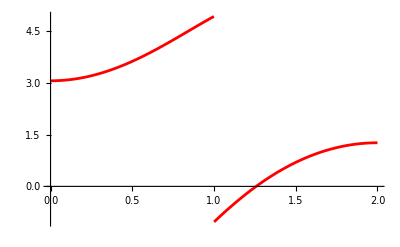

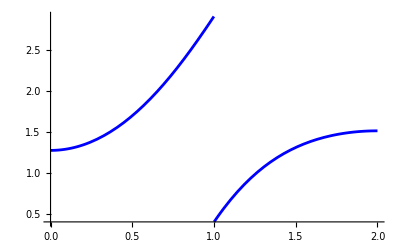

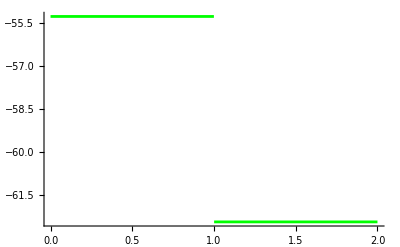

```mathematica
Clear[pl1,pl2,pl3] 
pl1=Plot[Cθ1idN,{t,0,2},PlotRange->All,PlotStyle->Red] 
pl2=Plot[Cθ2idN,{t,0,2},PlotStyle->Blue] 
pl3=Plot[FidN,{t,0,2},PlotStyle->Green]
```